## E = E ẑ, B = B ẑ

```mathematica
em=υ/2(B e kz vf χ)/(kx^2+ky^2+kz^2);
FullSimplify[Grad[em,{kx,ky,kz}]/.{kx->k Cos[ϕ] Sin[θ],ky->k Sin[θ] Sin[ϕ],kz->k Cos[θ]}]
```

{-(B e vf υ χ Cos[θ] Cos[ϕ] Sin[θ])/k^2,-(B e vf υ χ Cos[θ] Sin[θ] Sin[ϕ])/k^2,-(B e vf υ χ Cos[2 θ])/(2 k^2)}

```mathematica
FullSimplify[Solve[s vf k + c k k ==μ,k],ass]/.s^2->1
```

{{k→-(s vf+√(vf^2+4 c μ))/(2 c)},{k→(-s vf+√(vf^2+4 c μ))/(2 c)}}

```mathematica
Cos[2 θ]/2==Cos[θ]^2-(Cos[θ]^2+Sin[θ]^2)/2//FullSimplify
```

True

```mathematica
Clear[B,Be,e,μ,c,kx,ky,kz,s,cq,vf,k,v0,v1,v0dotΩ,vmdotΩ,enm,det];

(* c = cq vf *)
rep={vf->Subscript[v, 0],EF->μ,τrat->Subscript[τ, G]/τ,bc->ω,om->υ };
krep={k->(-vf+√vf √(vf+4 cq ϵ))/(2 cq vf)};
ass=Assumptions->{k,vf,cq,ϵ,μ, Ef,s,c}∈Reals && k>0 &&  c>0 && ϵ>0 && μ>0&& Ef>0 && vf>0;
Be={0,0,B};χ=1;
BdotΩ=-ζ(B s Cos[θ])/(2 k^2);cq=c/vf;
v0=(s vf+2 c k){Cos[ϕ] Sin[θ], Sin[θ] Sin[ϕ],Cos[θ]};
enm=υ(B e Cos[θ] vf)/(2 k);
vm={-(B e vf υ  Cos[ϕ] Sin[2θ])/(2 k^2),-(B e vf υ  Sin[2θ] Sin[ϕ])/(2 k^2),-(B e vf υ Cos[2 θ])/(2 k^2)};
v0dotΩ= -ζ(s vf+2 c k)/k^2;
vmdotΩ=υ ζ(B e s vf Cos[θ])/(2 k^4);
(*f0'[en0]=-δ[Subscript[ϵ, χ,s]-μ];f0''[en0]=-δ'[Subscript[ϵ, χ,s]-μ];f0^(3)[en0]=-δ''[Subscript[ϵ, χ,s]-μ];*)
det=(k^2 Sin[θ])/(√(vf^2+4 c ϵ))(* (k^2 Sin[θ])/(√vf √(vf+(4 c ϵ)/vf))*);
```

```mathematica
f=s v k+c k^2;
roots=Solve[f==μ,k]
der=D[f, k]/.k->(-s v+√(s^2 v^2+4 c μ))/(2 c)
```

{{k→(-s v-√(s^2 v^2+4 c μ))/(2 c)},{k→(-s v+√(s^2 v^2+4 c μ))/(2 c)}}

√(s^2 v^2+4 c μ)

## linear disp band

```mathematica
(* -Graphics-;
-Graphics- *)
```

```mathematica
(* zz comp, along with the Drude term:*)
Clear[cond0,cond1,cond2,c0,c1,c2, δ, δp, δpp,cc1,cc2,cc3,cc4,cc5];
Print["Drude: indep of B terms"];(* v03^2 δ[ϵminμ] *)
c0=v0[[3]] v0[[3]] δ;
cond0=e^2 τ Integrate[det c0 ,{θ,0,π}]//FullSimplify
Print["B terms from I1 & I2 "];
c1=Simplify[(2v0[[3]] vm[[3]]-e BdotΩ (v0[[3]])^2) δ e^2 τ+ enm (v0[[3]])^2  δp e^2 τ-enm (v0[[3]])^2 e BdotΩ  δp e^2 τ+2enm v0[[3]] vm[[3]] δp e^2 τ+(e BdotΩ v0[[3]]-vm[[3]])^2 δ e^2 τ+(enm^2 v0[[3]] v0[[3]])/2 δpp  e^2 τ+(* -Graphics--> *)B^2 τ e^4(v0dotΩ)^2 δ]/.χ^2->1;
cond1[ζ_,υ_]=FullSimplify[ Integrate[det c1,{θ,0,π}]]/.χ^2->1
fac=(B^2 e^4 vf^(3/2) τ)/(60  √(vf+4 cq ϵ));
cc1=SeriesCoefficient[cond1[ζ,υ]/fac,{δ,0,1},{δp,0,0},{δpp,0,0}];
cc2=SeriesCoefficient[cond1[ζ,υ]/fac,{δ,0,0},{δp,0,1},{δpp,0,0}];
cc3=SeriesCoefficient[cond1[ζ,υ]/fac,{δ,0,0},{δp,0,0},{δpp,0,1}];
cc1 δ+cc2 δp+cc3 δpp==cond1[ζ,υ]/fac//FullSimplify
```

Drude: indep of B terms

(2 e^2 k^2 (2 c k+s vf)^2 δ τ)/(3 √(vf^2+4 c ϵ))

B terms from I1 & I2

1/(60 k^2 √(vf^2+4 c ϵ))B^2 e^4 τ (6 (20+s^2) (2 c k+s vf)^2 δ ζ^2+2 s vf (2 c k+s vf) (-2 δ+3 k (2 c k+s vf) δp) ζ υ+vf^2 (14 δ+k (2 c k+s vf) (-4 δp+3 k (2 c k+s vf) δpp)) υ^2)

True

```mathematica
Print["B terms from I3 and I4=I3"];
(* -Graphics-*)
c2=Simplify[
v0dotΩ(v0[[3]] +vm[[3]]-e v0[[3]]  BdotΩ)δ+v0[[3]]vmdotΩ δ+v0[[3]]enm v0dotΩ δp]/.χ^2->1;
cond2[ζ_,υ_]=2B τ e^3 Integrate[det c2,{θ,0,π}]//FullSimplify
fac=(B^2 e^4 vf^(3/2) τ)/(60  √(vf+4 cq ϵ));
cc4=SeriesCoefficient[cond2[ζ,υ]/fac,{δ,0,1},{δp,0,0},{δpp,0,0}];
cc5=SeriesCoefficient[cond2[ζ,υ]/fac,{δ,0,0},{δp,0,1},{δpp,0,0}];
cc4 δ+cc5 δp==cond2[ζ,υ]/fac//FullSimplify
```

B terms from I3 and I4=I3

-(2 B^2 e^4 (2 c k+s vf) ζ τ (s (2 c k+s vf) δ ζ+vf (δ-s δ+k (2 c k+s vf) δp) υ))/(3 k^2 √(vf^2+4 c ϵ))

True

```mathematica
(*Clear[int1];
intdrude(* divided by e^2 τ *)=FullSimplify[(2  k^2 (2 c k+s vf)^2)/(3 √(vf^2+4 c ϵ)) (* δ[ϵminμ] *)/.krep,Assumptions->ass]/.ϵ->μ
int1[ζ_,υ_,s_](* divided by e^2 τ *)=(B^2 e^2 vf^(3/2))/(60  √(vf+4 cq ϵ))FullSimplify[ cc1+cc4(*δ[ϵminμ]*)+(-1)D[ (cc2+cc5)((*fprime'[k]*)1)/(2 cq k vf+ vf),k](* δp[ϵminμ] *)+(-1)D[cc3(-2 cq(* fprime'[k]*))/((2 cq k+1)^3 vf^2)(*δpp[ϵminμ]*),k]+D[cc3((2 cq k+1) (*fprime''[k]*))/((2 cq k+1)^3 vf^2)(*δpp[ϵminμ]*),{k,2}]/.krep,Assumptions->ass]/.ϵ->μ*)
```

```mathematica
intdrude=(vf^2 (√vf-√(vf+(4 c μ)/vf))^2 ((-1+s) √vf+√(vf+(4 c μ)/vf))^2)/(6 c^2 √(vf^2+4 c μ));
```

```mathematica
int1[ζ_,υ_,s_]=(2 B^2 c^2 e^2 (64 c^3 (60+s (-20+3 s)) ζ^2 μ^3+32 c^2 vf^(3/2) ζ μ^2 √(vf+(4 c μ)/vf) ((-1+s) (60+s (-20+3 s)) ζ+(-10+9 s) υ)+8 c^2 vf^2 μ^2 (2 (4+(-2+s) s) (60+s (-20+3 s)) ζ^2+2 (40+3 s (-27+8 s)) ζ υ+7 υ^2)+4 c vf^(7/2) μ √(vf+(4 c μ)/vf) (4 (-1+s) (60+s (-20+3 s)) ζ^2+2 (-40+s (61+s (-26+3 s))) ζ υ+(7-4 s) υ^2)+vf^(11/2) √(vf+(4 c μ)/vf) (2 (-1+s) (60+s (-20+3 s)) ζ^2+2 (-30+s (52+s (-26+3 s))) ζ υ+(-2+(14-9 s) s) υ^2)+vf^6 ((2+(-2+s) s) (60+s (-20+3 s)) ζ^2+(60+s (-124+(50-3 s) s)) ζ υ+(9+s (-16+9 s)) υ^2)+2 c vf^4 μ (2 (5+2 (-2+s) s) (60+s (-20+3 s)) ζ^2+2 (100+s (-205+(74-3 s) s)) ζ υ+(16+s (-14+9 s)) υ^2)))/(15 vf^2 (vf^2+4 c μ)^(3/2) (vf+(4 c μ)/vf) (√vf-√(vf+(4 c μ)/vf))^2);
```

```mathematica
Clear[cfull,cbc,comm,cfull];
full[s_]=FullSimplify[Expand[ int1[1,1,s]]/.{s^4->1,s^2->1,s^3->2},Assumptions->ass];
cbc[s_]=(* BC-only, OMM turned off *)FullSimplify[Expand[ int1[1,0,s]]/.{s^4->1,s^2->1,s^3->2},Assumptions->ass];
comm[s_]=(* no pure BC *)Simplify[full[s]-cbc[s],Assumptions->ass];
cfull[bc_,om_,s_]=bc cbc[s]+om comm[s];
cfull[1,1,s]==cbc[s]+comm[s]//Simplify
cfull[1,1,s]==full[s]//Simplify
```

True

True

```mathematica
Clear[sumbc];
sumbc=FullSimplify[cbc[1]+cbc[-1],ass]
```

(2 B^2 c^2 e^2 (229 vf^2+252 c μ-166 vf √(vf^2+4 c μ)))/(15 √(vf^2+4 c μ) (vf^2+2 c μ-vf √(vf^2+4 c μ)))

## Plots

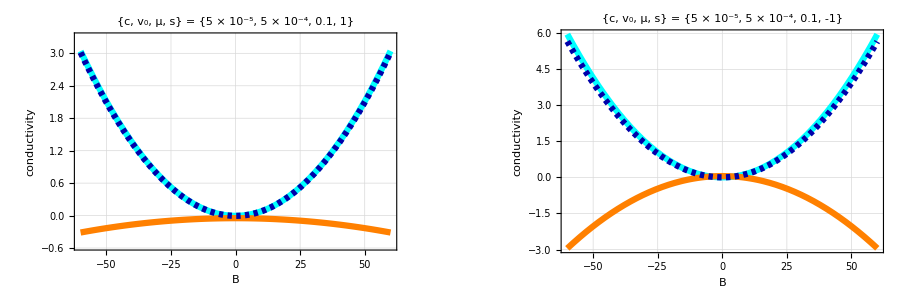

```mathematica
Clear[fn,f,μ,drude];e=1;
drude[μ_,vf_,c_,s_]=(vf^2 (√vf-√(vf+(4 c μ)/vf))^2 ((-1+s) √vf+√(vf+(4 c μ)/vf))^2)/(6 c^2 √(vf^2+4 c μ));
fn[B_,μ_,vf_,c_,{bc_,om_},s_]=(cfull[bc,om,s]+drude[μ,vf,c,s])/drude[μ+ 3*10^-7 s,vf,c,s]-1;
(************************)
style={Directive[Cyan,Thickness[0.01]],Directive[Orange,Thickness[0.01]],Directive[Darker[Blue],Dashing[0.007],Thickness[0.01]]};
mu=0.1-sval B 3*10^-7;cqval=5 10^-5;vfval= 5 10^-4;sc=10^3;
sval=1;
{fn[B,mu,vfval,cqval,{1,0},sval],fn[B,mu,vfval,cqval,{0,1},sval],fn[B,mu,vfval,cqval,{1,1},sval]}//Simplify//N;
(**)
g1=Plot[{fn[B,mu,vfval,cqval,{1,0},sval]sc,fn[B,mu,vfval,cqval,{0,1},sval]sc 10^1,fn[B,mu,vfval,cqval,{1,1},sval]sc},{B,-60,60},PlotRange->{-0.56,3.3},Frame->True,Axes->False,LabelStyle->{Black,Bold,22},FrameLabel->{"B","conductivity"},FrameTicksStyle->Directive[Darker[Gray],16],PlotLabel->Style["{c, v_0, μ, s} = {5 × 10^-5,  5 × 10^-4, 0.1, 1}",Bold,Darker[Brown],18],PlotStyle->style,ImageSize->450,GridLines->Automatic];
(*********)
sval=-1;
(*****)
g2=Plot[{fn[B,mu,vfval,cqval,{1,0},sval]sc,fn[B,mu,vfval,cqval,{0,1},sval]sc*10,fn[B,mu,vfval,cqval,{1,1},sval]sc},{B,-60,60},Frame->True,Axes->False,FrameTicksStyle->Directive[Darker[Gray],16],FrameLabel->{"B","conductivity"},LabelStyle->{Black,Bold,22},PlotLabel->Style["{c, v_0, μ, s} = {5 × 10^-5,  5 × 10^-4, 0.1, -1}",Bold,Darker[Brown],18],PlotStyle->style,ImageSize->450,GridLines->Automatic];
leg=LineLegend[style,{"δσ_zz^(bc, s) × 10^3","δσ_zz^(m, s) × 10^4","δσ_zz^(tot, s) × 10^3"},LabelStyle->{18,Darker[Brown],Bold},LegendLayout->{"Row",1}];
(***************)
pl=Legended[GraphicsGrid[{{g1,g2}},Spacings->{80,0},ImageSize->900],Placed[leg,Below]]
SetDirectory[NotebookDirectory[]];
Export["relax.pdf",Rasterize[pl],ImageResolution->900];
Clear[e];
```

```mathematica
cfull[1,0,s]/(B^2 e^2)/.rep;
TeXForm[%];
x=(2 c^2)/(15 √Subscript[v, 0] √((4 c μ)/Subscript[v, 0]+Subscript[v, 0]) (4 c μ+Subscript[v, 0]^2)^(5/2) (√Subscript[v, 0]-√((4 c μ)/Subscript[v, 0]+Subscript[v, 0]))^2);
Simplify[cfull[0,1,s]/(B^2 e^2 x)]/.rep
TeXForm[intdrude/.rep]
```

128 c^3 (-10+9 s) μ^3+16 c^2 (-133+136 s) μ^2 v_0^2+16 c (-56+59 s) μ v_0^4+(-111+118 s) v_0^6+216 c^2 (5-6 s) μ^2 v_0^(3/2) √((4 c μ)/v_0+v_0)+2 c (361-424 s) μ v_0^(7/2) √((4 c μ)/v_0+v_0)+2 (61-70 s) v_0^(11/2) √((4 c μ)/v_0+v_0)

\frac{v_0^2 \left(\sqrt{v_0}-\sqrt{\frac{4 c \mu }{v_0}+v_0}\right){}^2 \left(\sqrt{\frac{4 c \mu }{v_0}+v_0}+(s-1)
   \sqrt{v_0}\right){}^2}{6 c^2 \sqrt{4 c \mu +v_0^2}}

```mathematica
TeXForm[(B^2 e^4 τ)/(2π)^3]
```

\frac{B^2 e^4 \tau }{8 \pi ^3}